# Reconstruct Orbits from Symbols - Additional Sequences

Additional figures that were not selected for the paper

## Configuration A : Swapping 3 cores between 3 sequences with shared surrounding

```mathematica
s = 7;
int = s-4;
m =RandomInteger[{0,int},{29,21}];
```

From the m matrix defined above, we generate three matrices m1, m2, m3 identical, except to small submatrices B, C and D that are swapped between m1, m2 and m3. The blocks B (green), C (red) and D (cyan) is surrounded by a bigger frame A (blue) common to all three swapped sequences

```mathematica
pos1 = {2,1};
pos2 = {5,12};
pos3 = {17,8};

tout = 11;
nout = 8;
tin = 3;
nin = 2;
posin = {4,3};

{n1,n2,n3} = swapping3blocks[int,m,pos1,pos2,pos3,posin,tout,nout,tin,nin] ;

n1C= coloring2blocks[n1,pos1,posin,tout,nout,tin,nin,Blue,Green];
n1C = coloring2blocks[n1C,pos2,posin,tout,nout,tin,nin,Blue,Red];
n1C = coloring2blocks[n1C,pos3,posin,tout,nout,tin,nin,Blue,Cyan];

n2C= coloring2blocks[n2,pos1,posin,tout,nout,tin,nin,Blue,Red];
n2C = coloring2blocks[n2C,pos2,posin,tout,nout,tin,nin,Blue,Cyan];
n2C = coloring2blocks[n2C,pos3,posin,tout,nout,tin,nin,Blue,Green];

n3C= coloring2blocks[n3,pos1,posin,tout,nout,tin,nin,Blue,Cyan];
n3C = coloring2blocks[n3C,pos2,posin,tout,nout,tin,nin,Blue,Green];
n3C = coloring2blocks[n3C,pos3,posin,tout,nout,tin,nin,Blue,Red];

n1C // MatrixForm
n2C // MatrixForm
n3C // MatrixForm
```

(0 | 0 | 0 | 2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 1 | 3 | 0 | 1 | 2 | 2 | 0 | 1 | 2 | 1
0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 0 | 0
1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 0 | 1 | 2 | 3 | 0
1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 3 | 0 | 2 | 3 | 3 | 1 | 2 | 0 | 1 | 0
3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 2 | 3 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2
0 | 1 | 3 | 3 | 3 | 0 | 2 | 3 | 2 | 2 | 0 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 1
1 | 0 | 1 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 0 | 0
0 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 3 | 3
3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 1 | 1 | 0 | 1 | 3 | 0 | 0 | 0 | 2 | 3 | 1 | 0
0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 1 | 0 | 1 | 2 | 3 | 3 | 0 | 0 | 2 | 2
3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 1 | 0 | 1 | 0 | 1 | 3 | 1 | 0 | 2
1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2
0 | 3 | 1 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 3
3 | 0 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 3 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 0
2 | 1 | 2 | 2 | 3 | 2 | 0 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 2
1 | 2 | 2 | 1 | 0 | 1 | 1 | 0 | 3 | 0 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 1 | 0 | 1 | 1
3 | 0 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 3 | 1 | 2
2 | 0 | 2 | 2 | 2 | 1 | 3 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 0 | 2 | 0 | 2 | 0 | 3
3 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 1 | 0 | 0 | 2 | 3 | 0
0 | 3 | 2 | 0 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 0 | 2 | 2 | 2 | 1 | 1
2 | 1 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 3 | 1 | 1 | 0 | 2 | 3 | 1 | 2 | 0 | 3 | 2 | 3
3 | 1 | 3 | 3 | 2 | 3 | 1 | 1 | 0 | 1 | 3 | 0 | 3 | 0 | 0 | 2 | 1 | 0 | 1 | 3 | 0
3 | 3 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 0 | 2 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 2
2 | 1 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 3 | 2 | 3 | 0
2 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 2
0 | 3 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 3 | 0 | 2 | 1
2 | 0 | 2 | 1 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 1
0 | 0 | 0 | 3 | 1 | 2 | 0 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3
1 | 1 | 3 | 3 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 2 | 1)

(0 | 0 | 0 | 2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 1 | 3 | 0 | 1 | 2 | 2 | 0 | 1 | 2 | 1
0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 0 | 0
1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 0 | 1 | 2 | 3 | 0
1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 3 | 0 | 2 | 3 | 3 | 1 | 2 | 0 | 1 | 0
3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 2 | 3 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2
0 | 1 | 3 | 0 | 0 | 0 | 2 | 3 | 2 | 2 | 0 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 1
1 | 0 | 1 | 2 | 3 | 3 | 0 | 0 | 3 | 0 | 0 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 3 | 1 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 3 | 3
3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 1 | 1 | 0 | 1 | 3 | 1 | 1 | 0 | 2 | 3 | 1 | 0
0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 1 | 0 | 1 | 3 | 0 | 3 | 0 | 0 | 2 | 2
3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 1 | 0 | 2 | 1 | 1 | 3 | 1 | 0 | 2
1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2
0 | 3 | 1 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 3
3 | 0 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 3 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 0
2 | 1 | 2 | 2 | 3 | 2 | 0 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 2
1 | 2 | 2 | 1 | 0 | 1 | 1 | 0 | 3 | 0 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 1 | 0 | 1 | 1
3 | 0 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 3 | 1 | 2
2 | 0 | 2 | 2 | 2 | 1 | 3 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 0 | 2 | 0 | 2 | 0 | 3
3 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 1 | 0 | 0 | 2 | 3 | 0
0 | 3 | 2 | 0 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 0 | 2 | 2 | 2 | 1 | 1
2 | 1 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 3 | 3 | 3 | 0 | 2 | 3 | 1 | 2 | 0 | 3 | 2 | 3
3 | 1 | 3 | 3 | 2 | 3 | 1 | 1 | 0 | 1 | 0 | 0 | 3 | 0 | 0 | 2 | 1 | 0 | 1 | 3 | 0
3 | 3 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 2
2 | 1 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 3 | 2 | 3 | 0
2 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 2
0 | 3 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 3 | 0 | 2 | 1
2 | 0 | 2 | 1 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 1
0 | 0 | 0 | 3 | 1 | 2 | 0 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3
1 | 1 | 3 | 3 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 2 | 1)

(0 | 0 | 0 | 2 | 2 | 3 | 1 | 0 | 3 | 2 | 2 | 1 | 3 | 0 | 1 | 2 | 2 | 0 | 1 | 2 | 1
0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 0 | 0
1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 3 | 1 | 1 | 2 | 3 | 0 | 0 | 0 | 1 | 2 | 3 | 0
1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 3 | 0 | 2 | 3 | 3 | 1 | 2 | 0 | 1 | 0
3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 2 | 3 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2
0 | 1 | 3 | 1 | 1 | 0 | 2 | 3 | 2 | 2 | 0 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 3 | 1
1 | 0 | 1 | 3 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 0 | 0
0 | 1 | 0 | 2 | 1 | 1 | 3 | 1 | 3 | 1 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 3 | 3
3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 1 | 1 | 0 | 1 | 3 | 3 | 3 | 0 | 2 | 3 | 1 | 0
0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 1 | 0 | 1 | 0 | 0 | 3 | 0 | 0 | 2 | 2
3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 0 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 0 | 2
1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2
0 | 3 | 1 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 1 | 3
3 | 0 | 2 | 3 | 2 | 2 | 2 | 3 | 2 | 1 | 3 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 3 | 0
2 | 1 | 2 | 2 | 3 | 2 | 0 | 0 | 1 | 1 | 3 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 2
1 | 2 | 2 | 1 | 0 | 1 | 1 | 0 | 3 | 0 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 1 | 0 | 1 | 1
3 | 0 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3 | 3 | 0 | 1 | 0 | 0 | 3 | 2 | 1 | 3 | 1 | 2
2 | 0 | 2 | 2 | 2 | 1 | 3 | 1 | 0 | 0 | 0 | 3 | 2 | 1 | 2 | 0 | 2 | 0 | 2 | 0 | 3
3 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 1 | 0 | 0 | 2 | 3 | 0
0 | 3 | 2 | 0 | 0 | 3 | 0 | 3 | 2 | 2 | 3 | 1 | 0 | 3 | 1 | 0 | 2 | 2 | 2 | 1 | 1
2 | 1 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 3 | 0 | 0 | 0 | 2 | 3 | 1 | 2 | 0 | 3 | 2 | 3
3 | 1 | 3 | 3 | 2 | 3 | 1 | 1 | 0 | 1 | 2 | 3 | 3 | 0 | 0 | 2 | 1 | 0 | 1 | 3 | 0
3 | 3 | 0 | 3 | 2 | 2 | 2 | 0 | 1 | 0 | 1 | 0 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 2
2 | 1 | 2 | 0 | 0 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 3 | 0 | 3 | 0 | 2 | 3 | 2 | 3 | 0
2 | 1 | 2 | 0 | 0 | 0 | 3 | 0 | 2 | 0 | 3 | 2 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 2
0 | 3 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 0 | 2 | 3 | 0 | 2 | 1
2 | 0 | 2 | 1 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 1 | 2 | 3 | 1
0 | 0 | 0 | 3 | 1 | 2 | 0 | 1 | 2 | 1 | 2 | 1 | 3 | 2 | 1 | 0 | 2 | 0 | 0 | 3 | 3
1 | 1 | 3 | 3 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 2 | 1)

```mathematica
Evaluating and Plotting;
{Q1,P1} = Orbits[s,n1];
{Q2,P2} = Orbits[s,n2];
{Q3,P3} = Orbits[s,n3];
```

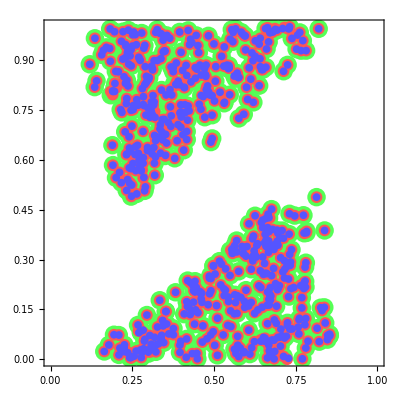

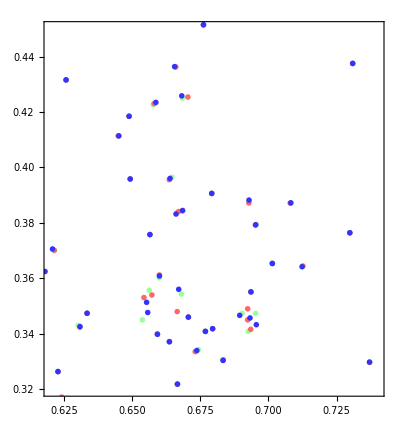

```mathematica
xplotrange = {0.62,0.74};
yplotrange = {0.32,0.45};

size1 = 19;
size2 = 12;
size3 = 8;
dgreen = 0.045;
dred = 0.022;
dblue = 0.011;

{plot3,plot4} = plotting3[Q1,P1,Q2,P2,Q3,P3,xplotrange,yplotrange,dgreen,dred,dblue,size1,size2,size3];
Show[plot3,ImageSize->400]
Show[plot4,ImageSize->400]
```

## Configuration B: Swapping two blocks

```mathematica
s = 13;
int = s-4;
m =RandomInteger[{0,int},{19,16}];
```

Here, we just switch two blocks between two matrices, identical on the outside of these blocks.

```mathematica
pos1 = {3,2};
pos2 = {12,9};
tout = 6;
nout = 4;

{o1,o2} = swapping1block[int,m,pos1,pos2,tout,nout] ;

o1C= coloring1block[o1,pos1,tout,nout,Green];
o1C = coloring1block[o1C,pos2,tout,nout,Red];

o2C = coloring1block[o2,pos1,tout,nout,Red];
o2C = coloring1block[o2C,pos2,tout,nout,Green];

o1C // MatrixForm
o2C // MatrixForm
```

(6 | 6 | 3 | 0 | 8 | 5 | 7 | 8 | 2 | 2 | 9 | 4 | 5 | 1 | 3 | 0
4 | 9 | 3 | 8 | 8 | 0 | 4 | 8 | 0 | 9 | 4 | 2 | 3 | 3 | 5 | 5
5 | 2 | 2 | 0 | 2 | 3 | 9 | 9 | 9 | 2 | 3 | 8 | 2 | 9 | 4 | 6
1 | 5 | 3 | 5 | 4 | 4 | 4 | 3 | 6 | 0 | 7 | 4 | 1 | 9 | 8 | 8
5 | 2 | 0 | 4 | 8 | 4 | 8 | 5 | 7 | 4 | 9 | 2 | 7 | 4 | 1 | 0
8 | 9 | 9 | 2 | 5 | 4 | 4 | 7 | 2 | 2 | 3 | 8 | 0 | 4 | 6 | 5
3 | 2 | 8 | 2 | 0 | 3 | 7 | 9 | 6 | 5 | 8 | 3 | 8 | 2 | 2 | 1
5 | 1 | 6 | 9 | 7 | 4 | 1 | 4 | 2 | 3 | 5 | 3 | 9 | 3 | 2 | 1
9 | 5 | 6 | 8 | 3 | 1 | 0 | 3 | 6 | 6 | 4 | 8 | 9 | 9 | 4 | 7
2 | 5 | 3 | 8 | 8 | 7 | 7 | 2 | 5 | 4 | 5 | 4 | 6 | 1 | 0 | 0
2 | 3 | 3 | 8 | 2 | 6 | 5 | 3 | 0 | 6 | 3 | 1 | 5 | 2 | 5 | 4
1 | 1 | 6 | 9 | 8 | 4 | 2 | 5 | 4 | 1 | 7 | 4 | 1 | 4 | 5 | 2
1 | 3 | 5 | 4 | 1 | 1 | 6 | 8 | 9 | 0 | 3 | 4 | 0 | 4 | 2 | 3
3 | 6 | 2 | 2 | 4 | 1 | 2 | 6 | 4 | 7 | 4 | 8 | 1 | 5 | 0 | 1
2 | 3 | 9 | 3 | 8 | 4 | 6 | 4 | 6 | 0 | 5 | 0 | 1 | 4 | 2 | 0
5 | 8 | 8 | 6 | 6 | 7 | 9 | 2 | 6 | 9 | 9 | 8 | 1 | 2 | 8 | 7
5 | 5 | 7 | 6 | 6 | 3 | 5 | 6 | 0 | 2 | 3 | 6 | 0 | 5 | 9 | 2
4 | 9 | 2 | 6 | 3 | 4 | 2 | 3 | 7 | 9 | 4 | 0 | 1 | 0 | 1 | 8
8 | 6 | 2 | 0 | 7 | 8 | 1 | 7 | 5 | 7 | 3 | 7 | 6 | 1 | 2 | 3)

(6 | 6 | 3 | 0 | 8 | 5 | 7 | 8 | 2 | 2 | 9 | 4 | 5 | 1 | 3 | 0
4 | 9 | 3 | 8 | 8 | 0 | 4 | 8 | 0 | 9 | 4 | 2 | 3 | 3 | 5 | 5
5 | 4 | 1 | 7 | 4 | 3 | 9 | 9 | 9 | 2 | 3 | 8 | 2 | 9 | 4 | 6
1 | 9 | 0 | 3 | 4 | 4 | 4 | 3 | 6 | 0 | 7 | 4 | 1 | 9 | 8 | 8
5 | 4 | 7 | 4 | 8 | 4 | 8 | 5 | 7 | 4 | 9 | 2 | 7 | 4 | 1 | 0
8 | 6 | 0 | 5 | 0 | 4 | 4 | 7 | 2 | 2 | 3 | 8 | 0 | 4 | 6 | 5
3 | 6 | 9 | 9 | 8 | 3 | 7 | 9 | 6 | 5 | 8 | 3 | 8 | 2 | 2 | 1
5 | 0 | 2 | 3 | 6 | 4 | 1 | 4 | 2 | 3 | 5 | 3 | 9 | 3 | 2 | 1
9 | 5 | 6 | 8 | 3 | 1 | 0 | 3 | 6 | 6 | 4 | 8 | 9 | 9 | 4 | 7
2 | 5 | 3 | 8 | 8 | 7 | 7 | 2 | 5 | 4 | 5 | 4 | 6 | 1 | 0 | 0
2 | 3 | 3 | 8 | 2 | 6 | 5 | 3 | 0 | 6 | 3 | 1 | 5 | 2 | 5 | 4
1 | 1 | 6 | 9 | 8 | 4 | 2 | 5 | 2 | 2 | 0 | 2 | 1 | 4 | 5 | 2
1 | 3 | 5 | 4 | 1 | 1 | 6 | 8 | 5 | 3 | 5 | 4 | 0 | 4 | 2 | 3
3 | 6 | 2 | 2 | 4 | 1 | 2 | 6 | 2 | 0 | 4 | 8 | 1 | 5 | 0 | 1
2 | 3 | 9 | 3 | 8 | 4 | 6 | 4 | 9 | 9 | 2 | 5 | 1 | 4 | 2 | 0
5 | 8 | 8 | 6 | 6 | 7 | 9 | 2 | 2 | 8 | 2 | 0 | 1 | 2 | 8 | 7
5 | 5 | 7 | 6 | 6 | 3 | 5 | 6 | 1 | 6 | 9 | 7 | 0 | 5 | 9 | 2
4 | 9 | 2 | 6 | 3 | 4 | 2 | 3 | 7 | 9 | 4 | 0 | 1 | 0 | 1 | 8
8 | 6 | 2 | 0 | 7 | 8 | 1 | 7 | 5 | 7 | 3 | 7 | 6 | 1 | 2 | 3)

```mathematica
Evaluating and Plotting;
{Q1,P1} = Orbits[s,o1];
{Q2,P2} = Orbits[s,o2];
```

```mathematica
(*xplotrange = {0.55,0.61};
yplotrange = {0.16,0.21};

sizeg1 = 13;
dgreen = 0.04;
dred = 0.015;

{plot3,plot4} = plotting2[Q1,P1,Q2,P2,xplotrange,yplotrange,dgreen,dred,sizeg1];
plot3
plot4*)
```

## Configuration C: Swapping 2 diamond-shaped cores between 2 sequences with shared diamond-shaped surrounding

```mathematica
s = 7;
int = s-4;
m =RandomInteger[{0,int},{30,29}];
```

Here, we just switch two diamond-shaped blocks between two sequences, with identical bordering on the outside of these blocks. From the m matrix defined above, we generate two matrices m1 and m2, identical, except to small diamond-shaped submatrices B and C that are interchanged between m1 and m2. The blocks B (green) and C (red) on both matrices are always surrounded by a bigger diamond-shaped “frame” A (blue).

```mathematica
pos1 = {2,10};
pos2 = {15,18};
dout = 8;
din = 2;

{m1,m2} = swapping2diamonds[int,m,dout,din,pos1,pos2] ;

m1C= coloringdiamond[m1,dout,din,pos1,Blue,Red];
m1C = coloringdiamond[m1C,dout,din,pos2,Blue,Green];

m2C = coloringdiamond[m2,dout,din,pos1,Blue,Green];
m2C = coloringdiamond[m2C,dout,din,pos2,Blue,Red];

m1C // MatrixForm
m2C // MatrixForm
```

(1 | 2 | 2 | 0 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 1 | 1 | 3
1 | 0 | 3 | 0 | 3 | 3 | 1 | 0 | 2 | 0 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 1 | 1 | 3 | 1 | 2 | 1 | 0
2 | 3 | 0 | 3 | 0 | 3 | 2 | 0 | 3 | 2 | 3 | 2 | 0 | 2 | 1 | 2 | 1 | 3 | 2 | 2 | 0 | 1 | 1 | 2 | 3 | 2 | 0 | 3 | 3
2 | 3 | 2 | 1 | 0 | 0 | 2 | 2 | 3 | 0 | 3 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 0 | 3 | 0 | 2 | 2
2 | 1 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 2 | 0 | 2 | 0 | 1 | 0 | 0 | 1 | 3 | 2 | 3 | 3 | 1 | 3 | 0 | 3 | 1 | 2 | 3 | 0
3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 1 | 2 | 2 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 3 | 1 | 1 | 3 | 0 | 1
0 | 2 | 2 | 3 | 3 | 0 | 3 | 1 | 3 | 2 | 1 | 0 | 2 | 3 | 2 | 0 | 0 | 1 | 0 | 3 | 0 | 3 | 2 | 0 | 3 | 3 | 2 | 3 | 2
0 | 3 | 0 | 3 | 2 | 1 | 2 | 3 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 1 | 2 | 1 | 1 | 0 | 1 | 2 | 1 | 1 | 2 | 0 | 2
1 | 3 | 2 | 0 | 1 | 0 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 3 | 1 | 2 | 2 | 1
0 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 0 | 0 | 3 | 3 | 1 | 2 | 1 | 1 | 0 | 0 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2
0 | 3 | 3 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 1 | 3 | 0 | 1 | 0 | 2 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 2 | 0
0 | 1 | 3 | 0 | 1 | 0 | 3 | 1 | 0 | 2 | 2 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 3 | 1 | 1 | 1 | 2 | 0 | 3
2 | 0 | 3 | 0 | 1 | 2 | 3 | 2 | 0 | 2 | 3 | 3 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 1 | 1 | 3 | 1 | 0 | 0 | 0 | 3 | 2
3 | 3 | 2 | 1 | 3 | 2 | 1 | 2 | 0 | 0 | 1 | 2 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 1 | 1 | 2 | 0 | 2 | 2 | 3 | 2 | 3
1 | 1 | 1 | 2 | 0 | 1 | 1 | 3 | 2 | 1 | 1 | 2 | 3 | 0 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 0 | 1 | 3 | 3 | 1 | 0
3 | 0 | 3 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 1 | 3 | 0 | 0 | 3 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 1 | 0 | 3 | 0
1 | 1 | 0 | 1 | 3 | 2 | 2 | 1 | 0 | 2 | 0 | 0 | 0 | 3 | 2 | 2 | 3 | 2 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 1 | 0 | 3 | 1
1 | 0 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 3 | 1 | 0 | 2 | 2
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 2 | 3 | 2 | 2 | 3 | 0 | 3 | 1 | 3 | 2 | 1 | 0 | 2 | 3 | 2 | 1 | 3 | 1 | 2 | 2 | 2
3 | 0 | 2 | 0 | 3 | 3 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 0 | 3 | 3 | 2 | 3 | 1 | 0 | 3
0 | 2 | 2 | 0 | 2 | 2 | 3 | 0 | 0 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 2 | 2 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 3 | 3 | 0 | 0
0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 2 | 3 | 1 | 0 | 1 | 0 | 1 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 1
3 | 2 | 1 | 1 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 1 | 0 | 3 | 1 | 1 | 0 | 0 | 3 | 3 | 1 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 1
1 | 1 | 0 | 0 | 2 | 1 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 0 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 1 | 3
0 | 2 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 2 | 2 | 3 | 2 | 3 | 3 | 1 | 0 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 0 | 2 | 2 | 3 | 0
1 | 1 | 1 | 0 | 2 | 3 | 1 | 0 | 3 | 1 | 2 | 1 | 2 | 3 | 2 | 2 | 0 | 2 | 3 | 3 | 1 | 0 | 0 | 1 | 0 | 3 | 0 | 1 | 2
2 | 2 | 0 | 2 | 1 | 2 | 1 | 3 | 0 | 2 | 3 | 0 | 2 | 3 | 3 | 2 | 0 | 0 | 1 | 2 | 1 | 0 | 2 | 3 | 2 | 1 | 3 | 2 | 2
3 | 0 | 0 | 2 | 2 | 1 | 0 | 3 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 0 | 1 | 1 | 3 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 3 | 1
2 | 1 | 3 | 0 | 1 | 3 | 2 | 0 | 3 | 1 | 1 | 3 | 2 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 1 | 3 | 1 | 2 | 3 | 2 | 2 | 1 | 2)

(1 | 2 | 2 | 0 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 1 | 0 | 1 | 0 | 2 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 1 | 1 | 3
1 | 0 | 3 | 0 | 3 | 3 | 1 | 0 | 2 | 0 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 1 | 1 | 3 | 1 | 2 | 1 | 0
2 | 3 | 0 | 3 | 0 | 3 | 2 | 0 | 3 | 2 | 3 | 2 | 0 | 2 | 1 | 2 | 1 | 3 | 2 | 2 | 0 | 1 | 1 | 2 | 3 | 2 | 0 | 3 | 3
2 | 3 | 2 | 1 | 0 | 0 | 2 | 2 | 3 | 0 | 3 | 2 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 0 | 3 | 0 | 2 | 2
2 | 1 | 3 | 1 | 3 | 2 | 2 | 2 | 3 | 2 | 0 | 2 | 0 | 1 | 0 | 0 | 1 | 3 | 2 | 3 | 3 | 1 | 3 | 0 | 3 | 1 | 2 | 3 | 0
3 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 1 | 2 | 2 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 3 | 1 | 1 | 3 | 0 | 1
0 | 2 | 2 | 3 | 3 | 0 | 3 | 1 | 3 | 2 | 1 | 0 | 2 | 3 | 2 | 0 | 0 | 1 | 0 | 3 | 0 | 3 | 2 | 0 | 3 | 3 | 2 | 3 | 2
0 | 3 | 0 | 3 | 2 | 1 | 2 | 3 | 0 | 1 | 1 | 3 | 1 | 0 | 3 | 3 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 2 | 2 | 1 | 2 | 1 | 3 | 2 | 2 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 1 | 2 | 1 | 1 | 0 | 1 | 2 | 1 | 1 | 2 | 0 | 2
1 | 3 | 2 | 0 | 1 | 0 | 1 | 3 | 1 | 3 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 3 | 1 | 2 | 2 | 1
0 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 0 | 0 | 3 | 3 | 1 | 2 | 1 | 1 | 0 | 0 | 2 | 3 | 2 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2
0 | 3 | 3 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 1 | 3 | 0 | 1 | 0 | 2 | 2 | 3 | 2 | 2 | 1 | 3 | 2 | 2 | 0
0 | 1 | 3 | 0 | 1 | 0 | 3 | 1 | 0 | 2 | 2 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 3 | 1 | 1 | 1 | 2 | 0 | 3
2 | 0 | 3 | 0 | 1 | 2 | 3 | 2 | 0 | 2 | 3 | 3 | 3 | 0 | 3 | 1 | 2 | 3 | 3 | 3 | 1 | 1 | 3 | 1 | 0 | 0 | 0 | 3 | 2
3 | 3 | 2 | 1 | 3 | 2 | 1 | 2 | 0 | 0 | 1 | 2 | 2 | 0 | 1 | 1 | 2 | 0 | 3 | 3 | 1 | 1 | 2 | 0 | 2 | 2 | 3 | 2 | 3
1 | 1 | 1 | 2 | 0 | 1 | 1 | 3 | 2 | 1 | 1 | 2 | 3 | 0 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 2 | 3 | 0 | 1 | 3 | 3 | 1 | 0
3 | 0 | 3 | 3 | 2 | 0 | 0 | 0 | 0 | 2 | 1 | 3 | 0 | 0 | 3 | 2 | 3 | 0 | 3 | 2 | 3 | 3 | 1 | 2 | 3 | 1 | 0 | 3 | 0
1 | 1 | 0 | 1 | 3 | 2 | 2 | 1 | 0 | 2 | 0 | 0 | 0 | 3 | 2 | 2 | 3 | 2 | 0 | 2 | 0 | 3 | 0 | 3 | 2 | 1 | 0 | 3 | 1
1 | 0 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 2 | 1 | 0 | 3 | 3 | 1 | 0 | 2 | 2
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 2 | 3 | 2 | 2 | 3 | 0 | 3 | 1 | 3 | 2 | 1 | 0 | 2 | 3 | 2 | 1 | 3 | 1 | 2 | 2 | 2
3 | 0 | 2 | 0 | 3 | 3 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 2 | 3 | 1 | 0 | 3
0 | 2 | 2 | 0 | 2 | 2 | 3 | 0 | 0 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 0 | 0 | 3 | 2 | 0 | 2 | 0 | 3 | 3 | 0 | 0
0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 2 | 3 | 1 | 0 | 1 | 0 | 1 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 0 | 0 | 2 | 2 | 2 | 2 | 1
3 | 2 | 1 | 1 | 3 | 3 | 2 | 0 | 0 | 0 | 2 | 1 | 0 | 3 | 1 | 1 | 0 | 0 | 3 | 3 | 1 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 1
1 | 1 | 0 | 0 | 2 | 1 | 3 | 2 | 3 | 3 | 0 | 0 | 1 | 0 | 2 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 1 | 3
0 | 2 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 2 | 2 | 3 | 2 | 3 | 3 | 1 | 0 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 0 | 2 | 2 | 3 | 0
1 | 1 | 1 | 0 | 2 | 3 | 1 | 0 | 3 | 1 | 2 | 1 | 2 | 3 | 2 | 2 | 0 | 2 | 3 | 3 | 1 | 0 | 0 | 1 | 0 | 3 | 0 | 1 | 2
2 | 2 | 0 | 2 | 1 | 2 | 1 | 3 | 0 | 2 | 3 | 0 | 2 | 3 | 3 | 2 | 0 | 0 | 1 | 2 | 1 | 0 | 2 | 3 | 2 | 1 | 3 | 2 | 2
3 | 0 | 0 | 2 | 2 | 1 | 0 | 3 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 0 | 1 | 1 | 3 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 3 | 1
2 | 1 | 3 | 0 | 1 | 3 | 2 | 0 | 3 | 1 | 1 | 3 | 2 | 3 | 0 | 2 | 0 | 0 | 0 | 3 | 1 | 3 | 1 | 2 | 3 | 2 | 2 | 1 | 2)

```mathematica
Evaluating and Plotting;
{Q1,P1} = Orbits[s,m1];
{Q2,P2} = Orbits[s,m2];
```

```mathematica
(*xplotrange = {0.3,0.41};
yplotrange = {0.08,0.20};

size1 = 17;
size2 = 10;
dgreen = 0.04;
dred = 0.015;

{plot3,plot4} = plotting2[Q1,P1,Q2,P2,xplotrange,yplotrange,dgreen,dred,size1,size2];
plot3
plot4*)
```

## Configuration D: Swapping 2 cores with shared surrounding and symbol coloring

```mathematica
s = 7;
int = s-4;
m1 =RandomInteger[{0,int},{27,28}];
m2 = RandomInteger[{0,int},{27,28}];
{T,Np} = Dimensions[m1];
```

Here, we have a common core, but the the surrounding of the matrix is different.

{RGBColor[0.772061, 0.92462, 0.998703],RGBColor[0.235431, 0.32765, 0.833291],RGBColor[0.16791, 0., 0.301671],RGBColor[0.16791, 0., 0.301671]}

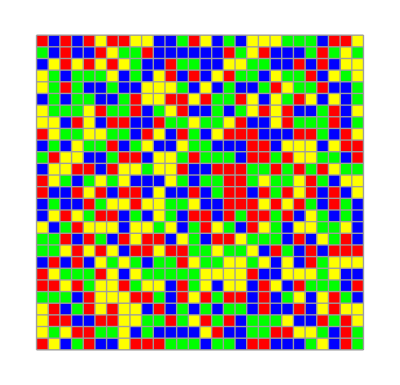

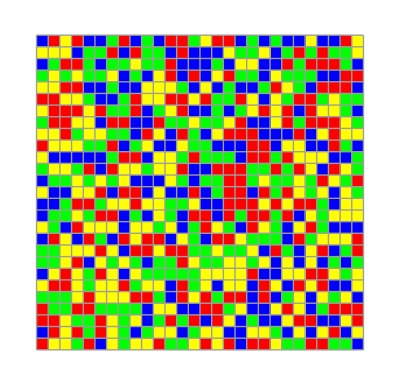

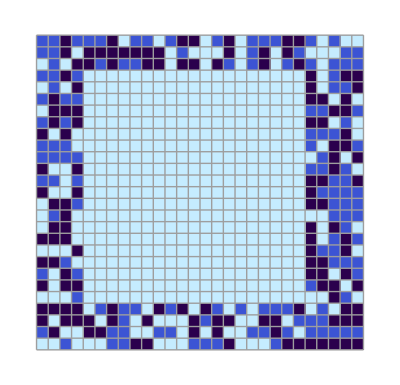

```mathematica
pos = {4,5};
tout = 20;
nout = 19;
tfac = 0;
nfac=0;
posbis = {tfac,nfac};

{o1,o2} = diffoutside[int,m1,m2,pos,tout,nout];

posbig1 = {pos[[2]]-1,T-pos[[1]]-tout+1};
posbig2 ={pos[[2]]+nout-1,T-pos[[1]]+1};
possmall1 = {pos[[2]]+nfac-1,T-pos[[1]]-tout+tfac+1};
possmall2 = {pos[[2]]+nout-nfac-1,T-pos[[1]]-tfac+1};

minb=1;
maxb=3;
cs="DeepSeaColors";
colorscheme=Table[ColorData[{cs,{minb,maxb}}][i],{i,0,int}]//Reverse

G3=Show[replacingsymbolswithsquares[o1,{Green,Yellow,Blue,Red}],drawingsquares[posbig1,posbig2,0.01]]
G4=Show[replacingsymbolswithsquares[o2,{Green,Yellow,Blue,Red}],drawingsquares[posbig1,posbig2,0.01]]
G5=Show[replacingsymbolswithsquares[Abs[o2-o1],colorscheme],drawingsquares[posbig1,posbig2,0.01,Black]]
```